# Take Home Exam - CS 298

## Kyle Perra - 7/19/15

I pledge that this submission is solely my work, and that I have neither given to nor received help from anyone other than the instructor.

## Free - Response Questions

1a) The Modeling Process:

● Analyze the problem
● Formulate a Model 
	Gather Data
	Make SimplifyingAssumptions
	Determine Variables and units Establish relationships among variables
● Solve the model (implement)
● Verify and Interpret
● Report on the model 

1b) Why Utilize Simulations?

	● For a particular phenemenon that may be too costly to operate or may be considered ‘mission-critical’ (such as rocket launches to the ISS), simulations offer the oportunity to examine in a controlled environment.
	● For a particular phenemenon that may span over a lengthy time period, simulations allow an opportunity to examine at a specified time rate.
	● For situations where outcomes are largely unknown and/or complex, simulations allow the ability to examine quantifiable, operational results.
	
2) How does Phyllotaxis relate to the Fibonacci sequence of numbers?
	
	Plants (and arguably all living things) are trying to optimize growth and
	increase their chance of survival. So, the placing of a leaf should be 		done so that the leaf least obscures the other leaves. Or, the placing of 	a seed should be done so that the seed least obscures all of the other 	seeds.
	
	The Golden Ratio (1.61803) is an irrational number, and is the best solution for plants attempting a rounded formation with minimal stacking of components (leafs) so as to avoid gaps. Aside from the Golden Ratio being able to be written in terms of itself (similar to the Fibonacci numbers), their ratio amounts are also similar when you take two successive Fibonacci numbers.

3) 
	In many (most?) scientific programs, there are repeated operations (loops) that are performed, and the accumulation of errors due to precision issues can lead to significant calculation errors -- accumulation errors. 

In one example, the Patriot Missile aresenal failed to operate after miscalculating system time. Specifically, the system (24 bit) kept track of time in tenths of a second - but since 1/10 is a never-ending decimal in binary, automatic round-offs occurred in increasing severity. Since the system relied on system time for its guidance system, after 100 hours of operation the arsenal failed to take down an incoming Russing scud missile in result of accumulating round-off errors. 

One example is: 
/* Code retrieved from StackOverflow user: Chris Vest
http://stackoverflow.com/questions/960072/rounding-errors */

public class Main {
  public static void main(String[] args) {
    double a = 0.7;
    double b = 0.9;
    double x = a + 0.1;
    double y = b - 0.1;
    System.out.println(x == y);
  }
}
This output will be false.

4a) Explain the utility of differential and difference equations:

Using either the differential or difference equation, the goal is to:
1. Collect Data
2. Determine Carrying Capacity (M)
3. Make forecast about a population 

As an example, in order to predict and forecast the size of a population, we need to determine the discrete change in the number of deaths and births, and the change in a population, from time (t-1) to time t (the current time)

4b) Why can difference equations lead to erroneous calculation results?

Differential equations deal with instantaneous rates of change, while difference
equations are for discrete simulations (and hence are approximations). As such, difference equations should be recognized as an insufficient means to calculate precise outputs (and especially in situations where sequential expressions are involved, i.e. the result of one item depends on the previous result of another item).

## Mathematica Basics

```mathematica
SetPrecision[N[Sin[15 Degree]],15]
```

0.258819045102521

```mathematica
N[CubeRoot[49]]
```

3.65931

```mathematica
p[t_]=14 t^3-12 t^2+2t-3
```

-3+2 t-12 t^2+14 t^3

```mathematica
p'[t]
```

2-24 t+42 t^2

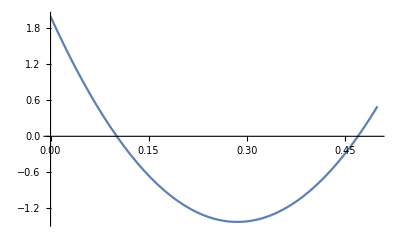

```mathematica
Plot[p'[t],{t,0,.5}]
```

In examining the graph, note that p’[t] is equal to 0 when x = 0.1 and x ~= 0.475

## Plotting/Manipulate

```mathematica
f[x_,y_]=x^y+13y-4x
```

-4 x+x^y+13 y

```mathematica
Manipulate[Plot[f[x,y],{x,0,10}],{y,1,21,2,Appearance ->"Labeled"}]
```

```mathematica
setTable=Table[f[x,y],{x,1,5},{y,1,5}]
```

{{10,23,36,49,62},{7,22,39,60,89},{4,23,54,121,296},{1,26,87,292,1073},{-2,31,144,657,3170}}

There is a value for which f[x,y] is negative (-2).

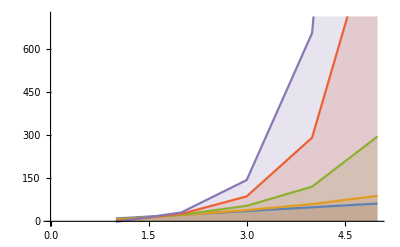

```mathematica
ListLinePlot[setTable,Filling->Axis]
```

## Word Problem

```mathematica
Clear[p,t,result]
```

```mathematica
result=DSolve[{p'[t]==-0.14p[t],p[0]==10^7},p[t],t]
```

{{p[t]→1.×10^7 ⅇ^(-0.14 t)}}

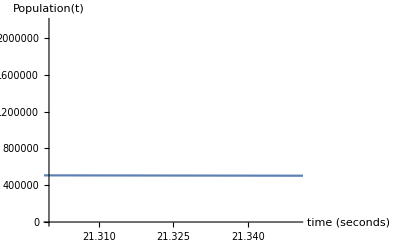

```mathematica
Plot[p[t]/.result,{t,0,100},AxesLabel->{"time (seconds)","Population(t)"},PlotRange->{{21.3,21.35},Automatic}]
```

The above graph indicates that the bacteria population will reach 500,000 at exactly 21.3 seconds.